# Phys130 Final Project Code Demo Tommy, Wen Chin.

## 1. Triangular Function

```mathematica
v=1; (*wave velocity*)
m=7*3; (*number of fourier terms,(4. needs m to be multiples of 3)*)
T=16; (*fundamental period*)
L=8; (*length*)
A1=1; (*amplitude*)
nlist=Table[i,{i,m}];
an1[n_]:=(32*((-1)^(n+1))*(1-Cos[((2*n-1)*Pi)/8]))/((2*n-1)*(2*n-1)*Pi*Pi)
un1[x_,t_,n_]:=an1[n]*Sin[((2*n-1)*Pi*x)/8]*Cos[((2*n-1)*Pi*v*t)/8]
u1[x_,t_]:=Sum[un1[x,t,n],{n,1,m}]
```

```mathematica
Animate[Plot[{Evaluate@Table[un1[x,t,n],{n,nlist}],u1[x,t]},{x,0,L},PlotRange->{-A1,A1},ImageSize->800],{t,0,T},AnimationRunning->False,AnimationRate->v/2]
```

```mathematica
b1=2; (*width*)
x01=0.5*L; (*position*)
f1[x_,x01_,b1_]:=UnitTriangle[(x-x01)/(0.5*b1)]
(2/L)*Integrate[f1[x,x01,b1]*Sin[(n*Pi*x)/L],{x,x01-0.5*b1,x01+0.5*b1}]
```

-(1.62114 (Sin[1.1781 n]-2. Sin[1.5708 n]+Sin[1.9635 n]))/n^2

```mathematica
anp1[n_]:=-(1.6211389382774044 (Sin[1.1780972450961724 n]-2. Sin[1.5707963267948966 n]+Sin[1.9634954084936207 n]))/n^2
```

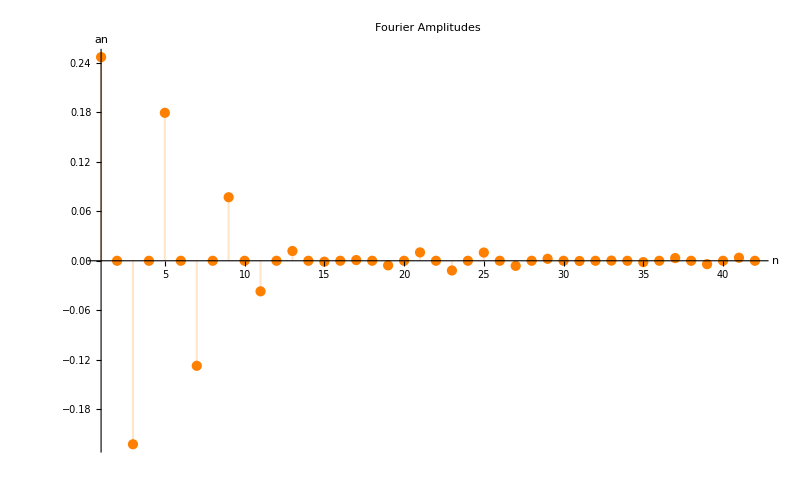

```mathematica
DiscretePlot[anp1[n],{n,2*m},PlotRange->All,AxesLabel->{"n","an"},PlotStyle->Orange,PlotLabel->"Fourier Amplitudes",ImageSize->800]
```

## 2. Rectangular Function

```mathematica
(4/L)*Integrate[Sin[((2*n-1)*Pi*x)/L],{x,3,4}]
```

(4 (-Sin[n π]+Sin[1/8 (π+6 n π)]))/((-1+2 n) π)

```mathematica
A2=1.11; (*amplitude*)
an2[n_]:=(4 (-Sin[n π]+Sin[1/8 (π+6 n π)]))/((-1+2 n) π)
un2[x_,t_,n_]:=an2[n]*Sin[((2*n-1)*Pi*x)/8]*Cos[((2*n-1)*Pi*v*t)/8]
u2[x_,t_]:=Sum[un2[x,t,n],{n,1,m}]
```

```mathematica
Animate[Plot[{Evaluate@Table[un2[x,t,n],{n,nlist}],u2[x,t]},{x,0,L},PlotRange->{-A2,A2},ImageSize->800],{t,0,T},AnimationRunning->False,AnimationRate->v/2]
```

```mathematica
(2/L)*Integrate[Sin[(n*Pi*x)/L],{x,x01-0.5*b1,x01+0.5*b1}]
```

(2.54648 Cos[(3 n π)/8]-2.54648 Cos[(5 n π)/8])/(4 n)

```mathematica
anp2[n_]:=(2.5464790894703255 Cos[(3 n π)/8]-2.5464790894703255 Cos[(5 n π)/8])/(4 n)
```

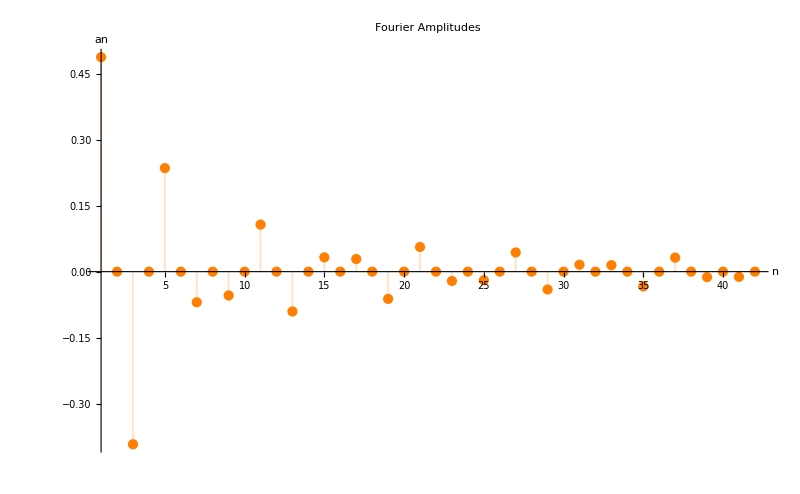

```mathematica
DiscretePlot[anp2[n],{n,2*m},PlotRange->All,AxesLabel->{"n","an"},PlotStyle->Orange,PlotLabel->"Fourier Amplitudes",ImageSize->800]
```

## 3. Triangular Function (offset)

```mathematica
b3=2; (*width*)
x03=2; (*position*)
f3[x_,x03_,b3_]:=UnitTriangle[(x-x03)/(0.5*b3)]
(2/L)*Integrate[f3[x,x03,b3]*Sin[(n*Pi*x)/L],{x,x03-0.5*b3,x03+0.5*b3}]
```

-(1.62114 (Sin[0.392699 n]-2. Sin[0.785398 n]+Sin[1.1781 n]))/n^2

```mathematica
an3[n_]:=-(1.6211389382774044 (Sin[0.39269908169872414 n]-2. Sin[0.7853981633974483 n]+Sin[1.1780972450961724 n]))/n^2
un3[x_,t_,n_]:=an3[n]*Sin[(n*Pi*x)/8]*Cos[(n*Pi*v*t)/8]
u3[x_,t_]:=Sum[un3[x,t,n],{n,1,m}]
```

```mathematica
Animate[Plot[{Evaluate@Table[un3[x,t,n],{n,nlist}],u3[x,t]},{x,0,L},PlotRange->{-A1,A1},ImageSize->800],{t,0,T},AnimationRunning->False,AnimationRate->v/2]
```

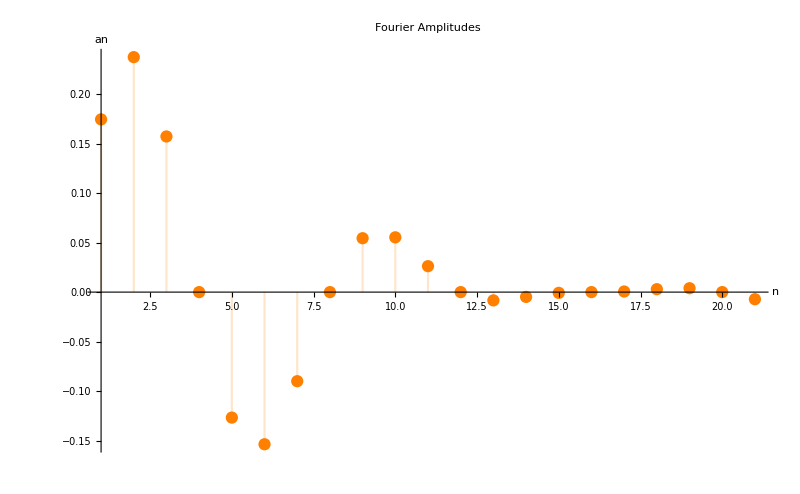

```mathematica
DiscretePlot[an3[n],{n,m},PlotRange->All,AxesLabel->{"n","an"},PlotStyle->Orange,PlotLabel->"Fourier Amplitudes",ImageSize->800]
```

## 4. Rectangular Function (offset)

```mathematica
(2/L)*Integrate[Sin[(n*Pi*x)/L],{x,x03-0.5*b3,x03+0.5*b3}]
```

(2.54648 Cos[(n π)/8]-2.54648 Cos[(3 n π)/8])/(4 n)

```mathematica
(*a_{multiples of 4} = 0*)
nOddlist=Table[i,{i,(2*m)/3}];
nEvenlist=Table[i,{i,m/3}];
anOdd4[n_]:=(2.5464790894703255 Cos[(5 (2n-1) π)/8]-2.5464790894703255 Cos[(7 (2n-1)π)/8])/(4 (2n-1))
anEven4[n_]:=(2.5464790894703255 Cos[(5 (4n-2) π)/8]-2.5464790894703255 Cos[(7 (4n-2)π)/8])/(4 (4n-2)) (*n=2,6,10*)
unOdd4[x_,t_,n_]:=anOdd4[n]*Sin[((2n-1)*Pi*x)/8]*Cos[((2n-1)*Pi*v*t)/8]
unEven4[x_,t_,n_]:=anEven4[n]*Sin[((4n-2)*Pi*x)/8]*Cos[((4n-2)*Pi*v*t)/8]
u4[x_,t_]:=Sum[unOdd4[x,t,n],{n,1,(2*m)/3}]+Sum[unEven4[x,t,n],{n,1,m/3}]
```

```mathematica
Animate[Plot[{Evaluate@Table[unOdd4[x,t,n],{n,nOddlist}],Evaluate@Table[unEven4[x,t,n],{n,nEvenlist}],u4[x,t]},{x,0,L},PlotRange->{-A2,A2},ImageSize->800],{t,0,T},AnimationRunning->False,AnimationRate->v/2]
```

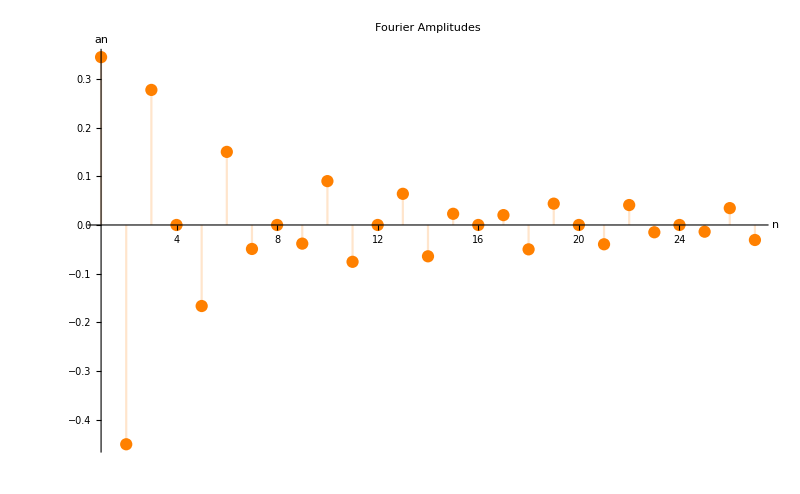

```mathematica
an4[n_]:=(2.5464790894703255 Cos[(5 n π)/8]-2.5464790894703255 Cos[(7 n π)/8])/(4 n)
DiscretePlot[an4[n],{n,m+6},PlotRange->All,AxesLabel->{"n","an"},PlotStyle->Orange,PlotLabel->"Fourier Amplitudes",ImageSize->800]
```